```mathematica
SameEdges[g_,h_]:=Block[{result=True},
If[EdgeCount[g]!=EdgeCount[h],Return[False]];
Table[If[!EdgeQ[g,e],result=False],{e,EdgeList[h]}];
result
]
```

```mathematica
SameVertices[g_,h_]:=Block[{result=True},
If[VertexCount[g]!=VertexCount[h],Return[False]];
Table[If[!VertexQ[g,v],result=False],{v,VertexList[h]}];
result
]
```

```mathematica
FindGraph[g_]:=Block[{isomorph},
isomorph=Select[Keys[stubbornForm4],
With[{h=stubbornForm4[#,"graph"]},
IsomorphicGraphQ[g,h]&&
SameEdges[g,h]&&
SameVertices[g,h]
]&];
First[isomorph]
]
```

```mathematica
FindGraph[CycleGraph[4]]
```

120

```mathematica
AddEdge[g_,code_,vertices_]:=Block[{h=g,decoded=PadLeft[IntegerDigits[code,2],3,0],i},
If[decoded[[1]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[2]]]];
If[decoded[[2]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[3]]]];
h
]
```

```mathematica
FindRelations[g_,verticesg_,h_,verticesh_]:=Block[{g2,h2,keyg,keyh},
Table[
g2=AddEdge[g,code,verticesg];
h2=AddEdge[h,code,verticesh];
keyg=FindGraph[g2];
keyh=FindGraph[h2];
(*Print[Graph[g2,VertexLabels->"Name"],keyg,Graph[h2,VertexLabels->"Name"],keyh];*)
{keyg,keyh}
,{code,0,7}
]
]
```

```mathematica
FindRelations[Graph[{1,2,3,4},{4<->1,4<->2}],{1,2,3},Graph[{1,2,3,4},{4<->1,4<->3}],{2,1,3}]
```

{{30,28},{39,109},{111,37},{120,118},{273,271},{282,352},{354,280},{363,361}}

```mathematica
stubbornForm4[4]["graph"]//EdgeList
```

{2<->4,3<->4}

```mathematica
repfours={z->Z,s01->x01,s02->x02,s03->x03,s04->x04,v01->y01,v02->y02,v03->y03,v04->y04,v05->y05,v06->y06,v07->y07,v10->y10,v11->y11,v12->y12}
```

{z→Z,s01→x01,s02→x02,s03→x03,s04→x04,v01→y01,v02→y02,v03→y03,v04→y04,v05→y05,v06→y06,v07→y07,v10→y10,v11→y11,v12→y12}

```mathematica
Compare4[number4_,number5_]:=Block[
{current4=stubbornForm4[number4],current5=stubbornForm4[number5], result={}, table4,table5, title, title2,cellformat},
table4=current4["colortable4"];
table5=current5["colortable4"];
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title=cellformat[With[{t=ToString[stubbornForm4[number4]["comp"]]},Style[stubbornForm4[number4]["colofour3"],If[t=="Greater",Darker[Darker[Green]],Red]]]];
title2=cellformat[With[{t=ToString[stubbornForm4[number5]["comp"]]},Style[stubbornForm4[number5]["colofour3"],If[t=="Greater",Darker[Darker[Green]],Red]]]];
Print[Labeled[
Graph[VertexList[current4["graph"]],EdgeList[current4["graph"]],
VertexCoordinates->{{-8.326672684688674*^-17,0.37317075685196444},{5.0*^-18,-0.1253658486296072},{0.9510565162951535,0.3090169943749475},{-1.8369701987210297*^-16,1.}},VertexLabels->{1->6,2->7,3->5,4->1} ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title,Style[number4,Bold,Underlined]},{Bottom,Top}]
->Labeled[
Graph[VertexList[current5["graph"]],EdgeList[current5["graph"]],VertexCoordinates->{{5.551115123125783*^-18,-0.1253658486296072},{-8.326672684688674*^-17,0.37317075685196444},{0.9510565162951535,0.3090169943749475},{0.5877852522924731,-0.8090169943749473}},VertexLabels->{1->7,2->6,3->5,4->4},ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title2,Style[number5,Bold,Underlined]},{Bottom,Top}]];
Table[
AppendTo[result,(table4[[ind[[1]],1]])==(table5[[ind[[2]],1]]/.repfours)];
AppendTo[result,(table4[[ind[[1]],2]])==(table5[[ind[[2]],2]]/.repfours)];,
{ind,{{1,1},{2,4},{4,2}}}
];
Print[ExpPrint[Fold[And,DeleteDuplicates[result]]]];
result
]
```

```mathematica
FindRelations[Graph[{1,2,3,4},{4<->1,4<->2}],{1,2,3},Graph[{1,2,3,4},{4<->1,4<->3}],{2,1,3}]
```

{{4,4},{37,13},{37,37},{120,40},{13,37},{40,40},{40,120},{121,121}}

```mathematica
{1,1},{3,2}
```

```mathematica
TableForm[stubbornForm4[30]["colortable4"]]
```

1/2 (-v01+v04+v06-v10) | v10
1/2 (6 s01+6 s02+4 s03+2 s04-v01-v02+v05+2 v06+v07-2 v11-2 v12) | 1/2 (-6 s01-6 s02-4 s03-2 s04+v02+v04-v05-v06-v07+v10+2 v11+2 v12)
0 | 1/2 (-v01+v04+v06+v10)
1/2 (2 s01+2 s03-v01+v04+v06+v10-2 v12) | -s01-s03+v12
0 | 1/2 (-v01+v04+v06+v10)
1/2 (10 s01+6 s02+6 s03+2 s04-2 v01-v02-2 v03-v04+3 v05+3 v06+v07+v10-2 v11-2 v12) | -5 s01-3 s02-3 s03-s04+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12

```mathematica
TableForm[stubbornForm4[28]["colortable4"]]
```

1/2 (-6 s01-4 s02-4 s03-2 s04+v01+2 v03+v04-2 v05-v06-v10+2 v12) | 1/2 (-2 s01-2 s02+v02+v04-v05-v06-v07+v10+2 v11)
1/2 (8 s01+6 s02+4 s03+2 s04-v01-v02+v05+2 v06+v07-2 v11-2 v12) | -8 s01-6 s02-4 s03-2 s04+v01+v02+v03+v04-2 v05-2 v06-v07+2 v11+2 v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
1/2 (2 s01+2 s03-v01+v04+v06+v10-2 v12) | 1/2 (-10 s01-6 s02-6 s03-2 s04+2 v01+v02+2 v03+v04-3 v05-3 v06-v07-v10+2 v11+4 v12)
s01+s03 | -5 s01-3 s02-3 s03-s04+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12

```mathematica
eqs=Flatten[Map[Compare4[#[[1]],#[[2]]]&,FindRelations[Graph[{1,2,3,4},{4<->1,4<->2}],{1,2,3},Graph[{1,2,3,4},{4<->1,4<->3}],{2,1,3}]]];
```

-Graphics-1/2 (-v01+v04+v06+v10)30→-Graphics-s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v1228

v10==1/2 (-2 x01-2 x02+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (-v01+v04+v06-v10)==1/2 (-6 x01-4 x02-4 x03-2 x04+y01+2 y03+y04-2 y05-y06-y10+2 y12)
-s01-s03+v12==-8 x01-6 x02-4 x03-2 x04+y01+y02+y03+y04-2 y05-2 y06-y07+2 y11+2 y12
1/2 (2 s01+2 s03-v01+v04+v06+v10-2 v12)==1/2 (8 x01+6 x02+4 x03+2 x04-y01-y02+y05+2 y06+y07-2 y11-2 y12)
1/2 (6 s01+6 s02+4 s03+2 s04-v01-v02+v05+2 v06+v07-2 v11-2 v12)==1/2 (2 x01+2 x03-y01+y04+y06+y10-2 y12)
1/2 (-6 s01-6 s02-4 s03-2 s04+v02+v04-v05-v06-v07+v10+2 v11+2 v12)==1/2 (-10 x01-6 x02-6 x03-2 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)

-Graphics--s01-s03+v1239→-Graphics--8 s01-6 s02-4 s03-2 s04+v01+v02+v03+v04-2 v05-2 v06-v07+2 v11+2 v12109

s02==1/2 (2 (x03+x04)-4 (x01+x02+x03+x04)+y02+y04-y05-y06-y07+y10+2 y11)
-s01-s03+v12==-8 x01-6 x02-4 x03-2 x04+y01+y02+y03+y04-2 y05-2 y06-y07+2 y11+2 y12
-s01-s02-s03+v12==1/2 (-12 x01-8 x02-6 x03-2 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)
1/2 (4 s01+4 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==1/2 (-4 x01-4 x02+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (-6 s01-4 s02-4 s03-2 s04+v02+v04-v05-v06-v07-v10+2 v11+2 v12)==1/2 (-12 x01-8 x02-8 x03-4 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)

-Graphics-1/2 (-6 s01-6 s02-4 s03-2 s04+v02+v04-v05-v06-v07+v10+2 v11+2 v12)111→-Graphics-1/2 (-10 s01-6 s02-6 s03-2 s04+2 v01+v02+2 v03+v04-3 v05-3 v06-v07-v10+2 v11+4 v12)37

-s02+v10==x01+x02+x03+x04
1/2 (2 (s03+s04)-4 (s01+s02+s03+s04)+v02+v04-v05-v06-v07+v10+2 v11)==x01+x02
-s01-s02-s03+v12==1/2 (-12 x01-8 x02-6 x03-2 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)
1/2 (-6 s01-4 s02-4 s03-2 s04+v02+v04-v05-v06-v07-v10+2 v11+2 v12)==1/2 (-12 x01-8 x02-8 x03-4 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)
1/2 (-6 s01-6 s02-4 s03-2 s04+v02+v04-v05-v06-v07+v10+2 v11+2 v12)==1/2 (-10 x01-6 x02-6 x03-2 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)

-Graphics--s01-s02-s03+v12120→-Graphics-1/2 (-12 s01-8 s02-6 s03-2 s04+2 v01+v02+2 v03+v04-3 v05-3 v06-v07-v10+2 v11+4 v12)118

1/2 (4 s01+2 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==x03+x04
-s01-s02-s03+v12==1/2 (-12 x01-8 x02-6 x03-2 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)
1/2 (-6 s01-4 s02-4 s03-2 s04+v02+v04-v05-v06-v07-v10+2 v11+2 v12)==1/2 (-12 x01-8 x02-8 x03-4 x04+2 y01+y02+2 y03+y04-3 y05-3 y06-y07-y10+2 y11+4 y12)

-Graphics-v10273→-Graphics-1/2 (-2 s01-2 s02+v02+v04-v05-v06-v07+v10+2 v11)271

-s02+v10==x01+x02+x03+x04
v10==1/2 (-2 x01-2 x02+y02+y04-y05-y06-y07+y10+2 y11)
s02==1/2 (2 (x03+x04)-4 (x01+x02+x03+x04)+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (2 (s03+s04)-4 (s01+s02+s03+s04)+v02+v04-v05-v06-v07+v10+2 v11)==x01+x02
1/2 (4 s01+4 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==1/2 (-4 x01-4 x02+y02+y04-y05-y06-y07+y10+2 y11)

-Graphics-1/2 (4 s01+4 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)282→-Graphics-1/2 (-4 s01-4 s02+v02+v04-v05-v06-v07+v10+2 v11)352

1/2 (4 s01+2 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==x03+x04
s02==1/2 (2 (x03+x04)-4 (x01+x02+x03+x04)+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (4 s01+4 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==1/2 (-4 x01-4 x02+y02+y04-y05-y06-y07+y10+2 y11)

-Graphics--s02+v10354→-Graphics-s01+s02+s03+s04280

-s02+v10==x01+x02+x03+x04
1/2 (4 s01+2 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)==x03+x04
1/2 (2 (s03+s04)-4 (s01+s02+s03+s04)+v02+v04-v05-v06-v07+v10+2 v11)==x01+x02

-Graphics-1/2 (4 s01+2 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)363→-Graphics-s03+s04361

x03+x04
1/2 (4 s01+2 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)

```mathematica
ExpressionToTableLoc[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
ExpressionToTableLoc[Simplify[Fold[And,eqs]]]
```

s02+x01+x02+x03+x04==v10
2 v10+2 x01+2 x02+y05+y06+y07==y02+y04+y10+2 y11
2 s02+4 x01+4 x02+2 x03+2 x04+y05+y06+y07==y02+y04+y10+2 y11
4 s01+4 s02+2 s03+2 s04+v05+v06+v07+2 x01+2 x02==v02+v04+v10+2 v11
4 s01+2 s02+2 s03+2 s04+v05+v06+v07+v10==v02+v04+2 (v11+x03+x04)
v01+v10+y01+2 y03+y04+2 y12==v04+v06+6 x01+4 x02+4 x03+2 x04+2 y05+y06+y10
s01+s03+y01+y02+y03+y04+2 y11+2 y12==v12+8 x01+6 x02+4 x03+2 x04+2 y05+2 y06+y07
6 s01+6 s02+4 s03+2 s04+v05+2 v06+v07+y01+2 y12==v01+v02+2 v11+2 v12+2 x01+2 x03+y04+y06+y10
2 s01+2 s03+v04+v06+v10+y01+y02+2 y11+2 y12==v01+2 v12+8 x01+6 x02+4 x03+2 x04+y05+2 y06+y07
2 s01+2 s02+2 s03+2 y01+y02+2 y03+y04+2 y11+4 y12==2 v12+12 x01+8 x02+6 x03+2 x04+3 y05+3 y06+y07+y10
4 s01+4 s02+2 s03+2 s04+v05+v06+v07+v10+4 x01+4 x02+y05+y06+y07==v02+v04+2 v11+y02+y04+y10+2 y11
6 s01+6 s02+4 s03+2 s04+v05+v06+v07+2 y01+y02+2 y03+y04+2 y11+4 y12==v02+v04+v10+2 v11+2 v12+10 x01+6 x02+6 x03+2 x04+3 y05+3 y06+y07+y10
6 s01+4 s02+4 s03+2 s04+v05+v06+v07+v10+2 y01+y02+2 y03+y04+2 y11+4 y12==v02+v04+2 v11+2 v12+12 x01+8 x02+8 x03+4 x04+3 y05+3 y06+y07+y10

```mathematica
Reduce[Fold[And,eqs],{s01}]//ExpressionToTableLoc
```

v10==-x01-x02+y02/2+y04/2-y05/2-y06/2-y07/2+y10/2+y11
s02==-2 x01-2 x02-x03-x04+y02/2+y04/2-y05/2-y06/2-y07/2+y10/2+y11
v01==v04+v06+7 x01+5 x02+4 x03+2 x04-y01-y02/2-2 y03-(3 y04)/2+(5 y05)/2+(3 y06)/2+y07/2+y10/2-y11-2 y12
s01==-s04+v02/2+v04/2-v05/2-v06/2-v07/2+v11-v12-(11 x01)/2-(7 x02)/2-2 x03+y01+y02/4+y03+y04/4-(5 y05)/4-(5 y06)/4-y07/4-(3 y10)/4+y11/2+2 y12
s03==s04-v02/2-v04/2+v05/2+v06/2+v07/2-v11+2 v12+(27 x01)/2+(19 x02)/2+6 x03+2 x04-2 y01-(5 y02)/4-2 y03-(5 y04)/4+(13 y05)/4+(13 y06)/4+(5 y07)/4+(3 y10)/4-(5 y11)/2-4 y12

```mathematica
Simplify[-s04+v02/2+v04/2-v05/2-v06/2-v07/2+v11-v12-(11 x01)/2-(7 x02)/2-2 x03+y01+y02/4+y03+y04/4-(5 y05)/4-(5 y06)/4-y07/4-(3 y10)/4+y11/2+2 y12==0]
```

4 s04+2 v05+2 v06+2 v07+4 v12+22 x01+14 x02+8 x03+5 y05+5 y06+y07+3 y10==2 v02+2 v04+4 v11+4 y01+y02+4 y03+y04+2 y11+8 y12

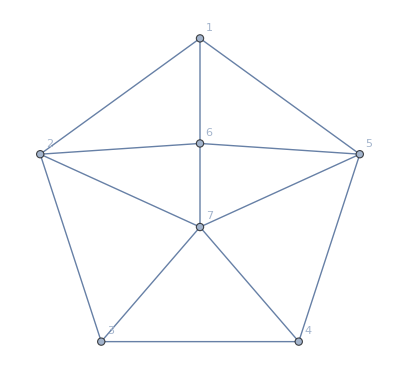

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]//GraphEmbedding
```

```mathematica
{{5.551115123125783*^-18,-0.1253658486296072},{-8.326672684688674*^-17,0.37317075685196444},{0.9510565162951535,0.3090169943749475},{0.5877852522924731,-0.8090169943749473}}
```

```mathematica
{{-8.326672684688674*^-17,0.37317075685196444},{5.551115123125783*^-18,-0.1253658486296072},{0.9510565162951535,0.3090169943749475},{-1.8369701987210297*^-16,1.}}
```

{{-1.83697×10^-16,1.},{-0.951057,0.309017},{-0.587785,-0.809017},{0.587785,-0.809017},{0.951057,0.309017},{-8.32667×10^-17,0.373171},{5.55112×10^-18,-0.125366}}